### Integrating the Fourier-Bessel transform for the exponentially decaying spin-spin correlation

```mathematica
Assuming[p>0&&L>0,Integrate[ Exp[-R/L] Sin[p R]/(p R)R^2 , {R,0, ∞}]]
```

(2 L^3)/((1+L^2 p^2)^2)

```mathematica
Series[1/((1+L^2 p^2)^2),{p,0,2}]
```

1-2 L^2 p^2+O[p]^3

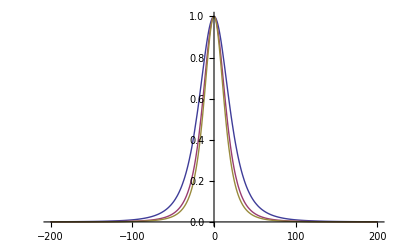

```mathematica
Rocking[Lc_,α_]:=1/((1+((2 π)/(671/532.)Lc α/1000.)^2)^2)
Plot[{Rocking[6,α],Rocking[8,α],Rocking[9,α]},{α,-200,200},PlotRange->All]
```

### Finding the proper way to compare AFM core results with Exponential decay results

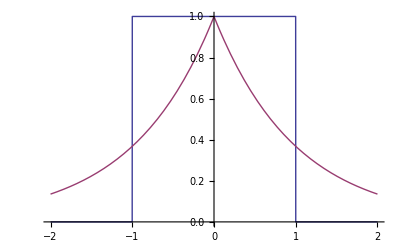

```mathematica
Plot[ {UnitBox[x/2], Exp[-Abs[x]]},{x,-2,2}]
```

```mathematica
Integrate[ UnitBox[x],{x,0,∞}]
```

1/2

```mathematica
Solve[1/2==Integrate[ Exp[-x],{x,0,y}],{y}]
```

{{y→ConditionalExpression[2 ⅈ π C[1]+Log[2],C[1]∈Integers]}}

```mathematica
Log[2.]
```

0.693147

```mathematica
Integrate[Exp[-x],{x,0,Log[2]}]
```

1/2

### Integrating the Fourier-Bessel Transform for the AFM core type spin spin correlations

```mathematica
Assuming[p>0&&L>0,Integrate[ UnitBox[R/L] Sin[p R]/(p R)R^2 , {R,0, ∞}]]
```

(-L p Cos[(L p)/2]+2 Sin[(L p)/2])/(2 p^3)

```mathematica
Assuming[p>0&&L>0,Integrate[ Sin[p R]/(p R)R^2 , {R,0, L}]]
```

(-L p Cos[L p]+Sin[L p])/p^3

```mathematica
Series[(-L p Cos[L p]+Sin[L p])/p^3 3/L^3,{p,0,2}]
```

1-(L^2 p^2)/10+O[p]^3

```mathematica
ExpDecay[L_,p_]:=1/((1+L^2 p^2)^2)
AFMCore[L_,p_]:=(-L p Cos[L p]+Sin[L p])/p^3/(L^3/3)
```

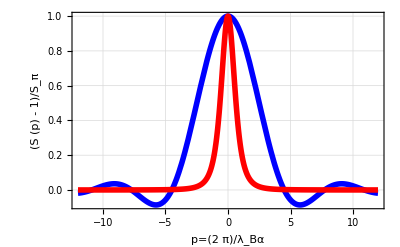

/home/pmd/sandbox/bragg/rockint-analytic

rocking-fourier.png

```mathematica
g1=Plot[{AFMCore[1.,p],ExpDecay[1.,p]},{p,-12,12},Frame->True, PlotRange->All,
FrameStyle->Thickness[0.008],
PlotStyle->{Directive[Thickness[0.01],Blue],Directive[Thickness[0.01],Red]},FrameLabel->{"p=(2  π)/λ_Bα","(S (p) - 1)/S_π",None,None},
GridLines->{Automatic,Automatic},
LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],RotateLabel->False]
SetDirectory[NotebookDirectory[]]
Export["rocking-fourier.png",g1,ImageResolution->180]
```

```mathematica
Limit[(-L p Cos[(L p)/2]+2 Sin[(L p)/2])/(2 p^3),p->0]
```

L^3/24

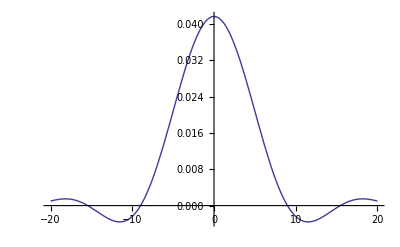

```mathematica
Plot[(-L p Cos[(L p)/2]+2 Sin[(L p)/2])/(2 p^3)/.L->1,{p,-20,20}]
```